```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->t]
```

```mathematica
T1[t_,m_]:= Module[{K=0*IdentityMatrix[m]},ReplacePart[K,Table[{x,x},{x,2,m,2}]->t]]
```

```mathematica
T2[t_,m_]:=t*IdentityMatrix[m]-T1[t,m]
```

```mathematica
Clear[LEFT]
```

```mathematica
leads =Table[ToExpression[Import["~/Downloads/PhD_new/PhD/fwi/AGNR/sudo_q/leads0001/lead_"<>ToString[x]<>"_.dat"]],{x,Range[0,3,0.01]}]
```

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=leads[[Round[ω*100+1]]](*Module[{J=Inverse[β[ω,0.001,1,0,m]],A:=Inverse[β[ω,0.001,1,0,m]],Ta:=T1[1,m],Tb= T2[1,m]},Do[J=Inverse[IdentityMatrix[m]-A.Tb.Inverse[IdentityMatrix[m]-A.Ta.J.Ta].A.Tb].A,5000];J=J]*)
```

```mathematica
f1[y_,start_,stop_]:=f1[y,start,stop]= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Clear[dist]
```

```mathematica
dist[total_,concentration_,area_]:=dist[total,concentration,area]=Table[SortBy[Join[RandomSample[Join[s[1,100,1,Round[area/2]]],concentration],RandomSample[Join[s[1,100,area-Round[area/2],area]],total-concentration]],First],10000]
```

```mathematica
f[ω_,δ_,t_,ϵ_,ϵ1_,area_,total_,concentration_,number_,unitcell_]:=Inverse[Module[{J=β[ω,δ,t,ϵ,area]},Do[J=Module[{m=unitcell},If[dist[total,concentration,area][[number]][[loc1,1]]==m,ReplacePart[J,{{dist[total,concentration,area][[number]][[loc1,2]],dist[total,concentration,area][[number]][[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]]
```

```mathematica
TL[t_,m_,area_]:=Module[{MAT=0*IdentityMatrix[area]},MAT[[1;;m,1;;m]]=T1[t,m];MAT]
```

```mathematica
TR[t_,m_,area_]:=Module[{MAT=0*IdentityMatrix[area]},MAT[[1;;m,1;;m]]=T1[t,m];MAT]
```

```mathematica
SLLEAD[ω_,m_,area_]:=Module[{MAT=0*IdentityMatrix[area]},MAT[[1;;m,1;;m]]=LEFT[ω,m];MAT]
```

```mathematica
SRLEAD[ω_,m_,area_]:=Module[{MAT=0*IdentityMatrix[area]},MAT[[1;;m,1;;m]]=LEFT[ω,m];MAT]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,total_,concentration_,number_,m_,area_]:= Module[{},
recurs=Module[{J1=SLLEAD[ω,m,area]},
Do[
J1=Inverse[IdentityMatrix[area]-f[ω,δ,t,ϵ,ϵ1,area,total,concentration,number,unitcell+1].T2[t,area].Inverse[IdentityMatrix[area]-f[ω,δ,t,ϵ,ϵ1,area,total,concentration,number,unitcell].T1[1,area].J1.T1[1,area]].f[ω,δ,t,ϵ,ϵ1,area,total,concentration,number,unitcell].T2[t,area]].f[ω,δ,t,ϵ,ϵ1,area,total,concentration,number,unitcell+1],{unitcell,1,100,2}];J1=J1];ir=Inverse[IdentityMatrix[area]-SRLEAD[ω,m,area].TR[1,m,area].recurs.TR[1,m,area]].SRLEAD[ω,m,area];il=Inverse[IdentityMatrix[area]-recurs.TR[1,m,area].SRLEAD[ω,m,area].TR[1,m,area]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.TR[1,m,area].recurs;
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.TR[1,m,area].grr1.TR[1,m,area]-TR[1,m,area].GNON1.TR[1,m,area].GNON1]];If[TRA>10,10,TRA]]
```

```mathematica
Clear[transmission]
```

```mathematica
ListLinePlot[ParallelTable[{ω,CA[ω,0.001,1,0,0.5,10,5,1,15,50]},{ω,Range[0,2,0.01]}]]
```

```mathematica
Table[Mean[ParallelTable[CA[0.74,0.001,1,0,1,100,x,NUM,15,50],{NUM,1000}]],{x,5,95,10}]
```

{3.1215,2.97995,2.86876,2.72364,2.6641,2.59142,2.53176,2.46739,2.463,2.40002}

```mathematica
transmission:=transmission=Monitor[Table[{x,Import["~/PhD_new/PhD/fwi/AGNR/sudo_q/new_total_100_lead_15_device_50_length_100_up_"<>ToString[x]<>"_.dat"]},{x,Range[10,60,10]}],x]
```

```mathematica
transmission
```

{{10,{{0.,0.365848},{0.01,0.239393},{0.02,0.181314},{0.03,0.175973},{0.04,0.121631},{0.05,0.115414},{0.06,0.131988},{0.07,0.115503},{0.08,0.15078},{0.09,0.359111},{0.1,0.199971},{0.11,0.272158},{0.12,0.342866},{0.13,0.138877},{0.14,0.405571},{0.15,0.607427},{0.16,0.40469},{0.17,0.546703},{0.18,0.45861},{0.19,0.513785},{0.2,0.517795},{0.21,0.399445},{0.22,0.442951},{0.23,0.525985},{0.24,0.360642},{0.25,0.371354},{0.26,0.650564},{0.27,0.452576},{0.28,0.852268},{0.29,0.82926},{0.3,0.732097},{0.31,1.05022},{0.32,0.987842},{0.33,1.05092},{0.34,0.983142},{0.35,1.17968},{0.36,1.00508},{0.37,1.13432},{0.38,0.872235},{0.39,0.973098},{0.4,0.740666},{0.41,0.840825},{0.42,1.03816},{0.43,1.39169},{0.44,1.60483},{0.45,1.65842},{0.46,1.85544},{0.47,1.90981},{0.48,1.87108},{0.49,1.98589},{0.5,2.02555},{0.51,1.98816},{0.52,1.95182},{0.53,1.99216},{0.54,2.04043},{0.55,1.96395},{0.56,1.92858},{0.57,1.8622},{0.58,1.6792},{0.59,1.54108},{0.6,1.26929},{0.61,1.31886},{0.62,1.33239},{0.63,1.27464},{0.64,1.31258},{0.65,1.53617},{0.66,1.79295},{0.67,1.65469},{0.68,1.95226},{0.69,2.17591},{0.7,2.64053},{0.71,2.83085},{0.72,2.92983},{0.73,2.96208},{0.74,3.06889},{0.75,3.04033},{0.76,3.09663},{0.77,3.23254},{0.78,3.23543},{0.79,3.17795},{0.8,3.22012},{0.81,3.1402},{0.82,3.23376},{0.83,3.21432},{0.84,2.71573},{0.85,2.49152},{0.86,3.28767},{0.87,3.50793},{0.88,3.78115},{0.89,3.91377},{0.9,3.99809},{0.91,4.10099},{0.92,4.1925},{0.93,4.12803},{0.94,4.25899},{0.95,4.19174},{0.96,3.15308},{0.97,3.73053},{0.98,4.15862},{0.99,4.11608},{1.,4.16438},{1.01,4.38172},{1.02,4.39452},{1.03,4.61611},{1.04,4.748},{1.05,4.77175},{1.06,4.80008},{1.07,4.6382},{1.08,4.46855},{1.09,4.37765},{1.1,4.39942},{1.11,4.39067},{1.12,4.42741},{1.13,4.45408},{1.14,4.49301},{1.15,4.50683},{1.16,4.57358},{1.17,4.60432},{1.18,4.62479},{1.19,4.57419},{1.2,4.45426},{1.21,4.36989},{1.22,4.30076},{1.23,4.30966},{1.24,4.31606},{1.25,4.32226},{1.26,4.32697},{1.27,4.32548},{1.28,4.33616},{1.29,4.37239},{1.3,4.34902},{1.31,4.29745},{1.32,4.16345},{1.33,4.02469},{1.34,3.94021},{1.35,3.82017},{1.36,3.71556},{1.37,3.55152},{1.38,3.29678},{1.39,2.57983},{1.4,3.07619},{1.41,3.35154},{1.42,3.58731},{1.43,3.75712},{1.44,3.76303},{1.45,3.78353},{1.46,3.83311},{1.47,3.81931},{1.48,3.89123},{1.49,3.92414},{1.5,3.93097},{1.51,3.98342},{1.52,4.00397},{1.53,4.03836},{1.54,4.05096},{1.55,4.08578},{1.56,4.0474},{1.57,3.97972},{1.58,3.95977},{1.59,3.9299},{1.6,3.928},{1.61,3.94825},{1.62,3.94694},{1.63,3.94377},{1.64,3.97411},{1.65,3.9642},{1.66,3.96246},{1.67,3.93928},{1.68,3.88187},{1.69,3.77562},{1.7,3.72889},{1.71,3.67442},{1.72,3.61416},{1.73,3.52433},{1.74,3.4646},{1.75,3.30976},{1.76,2.98428},{1.77,2.63976},{1.78,2.86597},{1.79,2.98747},{1.8,3.077},{1.81,3.12221},{1.82,3.17266},{1.83,3.23767},{1.84,3.25038},{1.85,3.30217},{1.86,3.34239},{1.87,3.37195},{1.88,3.42099},{1.89,3.44511},{1.9,3.41775},{1.91,3.40627},{1.92,3.37307},{1.93,3.35773},{1.94,3.34754},{1.95,3.36668},{1.96,3.37795},{1.97,3.37605},{1.98,3.40177},{1.99,3.39838},{2.,3.36077}}},{20,{{0.,0.422329},{0.01,0.515154},{0.02,0.317544},{0.03,0.225667},{0.04,0.208597},{0.05,0.14312},{0.06,0.129521},{0.07,0.105556},{0.08,0.150366},{0.09,0.297375},{0.1,0.17599},{0.11,0.236777},{0.12,0.363598},{0.13,0.163863},{0.14,0.370272},{0.15,0.607457},{0.16,0.407228},{0.17,0.50985},{0.18,0.376129},{0.19,0.489527},{0.2,0.499648},{0.21,0.332795},{0.22,0.44033},{0.23,0.445199},{0.24,0.441983},{0.25,0.378904},{0.26,0.624213},{0.27,0.370833},{0.28,0.808763},{0.29,0.773138},{0.3,0.698873},{0.31,1.01436},{0.32,0.911168},{0.33,1.00365},{0.34,1.00082},{0.35,1.1439},{0.36,0.954874},{0.37,1.1071},{0.38,0.806411},{0.39,0.913425},{0.4,0.72039},{0.41,0.818322},{0.42,0.961285},{0.43,1.33532},{0.44,1.51804},{0.45,1.62227},{0.46,1.78089},{0.47,1.88481},{0.48,1.81593},{0.49,1.93052},{0.5,1.97562},{0.51,1.92907},{0.52,1.92324},{0.53,1.94505},{0.54,1.96849},{0.55,1.8394},{0.56,1.86603},{0.57,1.74645},{0.58,1.60575},{0.59,1.51129},{0.6,1.19149},{0.61,1.40383},{0.62,1.25877},{0.63,1.26644},{0.64,1.27224},{0.65,1.45605},{0.66,1.74929},{0.67,1.56995},{0.68,1.85311},{0.69,2.07352},{0.7,2.51065},{0.71,2.70093},{0.72,2.7845},{0.73,2.80835},{0.74,2.94744},{0.75,2.92686},{0.76,2.99946},{0.77,3.12377},{0.78,3.1191},{0.79,3.06122},{0.8,3.12321},{0.81,2.99695},{0.82,3.13685},{0.83,3.03946},{0.84,2.48655},{0.85,2.31907},{0.86,3.05985},{0.87,3.28703},{0.88,3.52529},{0.89,3.71303},{0.9,3.74665},{0.91,3.87193},{0.92,3.97281},{0.93,3.93338},{0.94,4.09105},{0.95,3.99526},{0.96,2.98587},{0.97,3.50308},{0.98,3.86904},{0.99,3.87397},{1.,3.98189},{1.01,4.25},{1.02,4.24658},{1.03,4.43863},{1.04,4.55451},{1.05,4.61475},{1.06,4.65146},{1.07,4.42157},{1.08,4.25618},{1.09,4.15989},{1.1,4.16282},{1.11,4.19064},{1.12,4.20656},{1.13,4.25514},{1.14,4.29437},{1.15,4.33332},{1.16,4.37857},{1.17,4.3933},{1.18,4.41947},{1.19,4.37025},{1.2,4.22833},{1.21,4.14084},{1.22,4.0885},{1.23,4.10136},{1.24,4.10843},{1.25,4.09999},{1.26,4.13044},{1.27,4.12623},{1.28,4.14655},{1.29,4.14534},{1.3,4.12139},{1.31,4.06845},{1.32,3.94241},{1.33,3.79009},{1.34,3.63412},{1.35,3.57131},{1.36,3.4364},{1.37,3.29509},{1.38,3.05899},{1.39,2.38115},{1.4,2.83482},{1.41,3.1342},{1.42,3.32911},{1.43,3.45949},{1.44,3.55018},{1.45,3.56905},{1.46,3.59723},{1.47,3.64628},{1.48,3.67},{1.49,3.74057},{1.5,3.7625},{1.51,3.80164},{1.52,3.84963},{1.53,3.88817},{1.54,3.90692},{1.55,3.90929},{1.56,3.87528},{1.57,3.82017},{1.58,3.78135},{1.59,3.75785},{1.6,3.80623},{1.61,3.78979},{1.62,3.81349},{1.63,3.80002},{1.64,3.80829},{1.65,3.81273},{1.66,3.79418},{1.67,3.76473},{1.68,3.71414},{1.69,3.59708},{1.7,3.5373},{1.71,3.49819},{1.72,3.42074},{1.73,3.36074},{1.74,3.28642},{1.75,3.12621},{1.76,2.80525},{1.77,2.39282},{1.78,2.68699},{1.79,2.81732},{1.8,2.90262},{1.81,2.93754},{1.82,2.98323},{1.83,3.05194},{1.84,3.11074},{1.85,3.13908},{1.86,3.18387},{1.87,3.22585},{1.88,3.27071},{1.89,3.29315},{1.9,3.28207},{1.91,3.25845},{1.92,3.21332},{1.93,3.21435},{1.94,3.19862},{1.95,3.22132},{1.96,3.22854},{1.97,3.23635},{1.98,3.26239},{1.99,3.25939},{2.,3.26065}}},{30,{{0.,0.454177},{0.01,0.546163},{0.02,0.42579},{0.03,0.311123},{0.04,0.2172},{0.05,0.153688},{0.06,0.124501},{0.07,0.118369},{0.08,0.148073},{0.09,0.311774},{0.1,0.199394},{0.11,0.239922},{0.12,0.337511},{0.13,0.191389},{0.14,0.362677},{0.15,0.579697},{0.16,0.398258},{0.17,0.471945},{0.18,0.305362},{0.19,0.461614},{0.2,0.469712},{0.21,0.30504},{0.22,0.420399},{0.23,0.412664},{0.24,0.50807},{0.25,0.389739},{0.26,0.600734},{0.27,0.341509},{0.28,0.761414},{0.29,0.695409},{0.3,0.678092},{0.31,0.998231},{0.32,0.869935},{0.33,0.954656},{0.34,0.957527},{0.35,1.09126},{0.36,0.88615},{0.37,1.0506},{0.38,0.792074},{0.39,0.841015},{0.4,0.671412},{0.41,0.808725},{0.42,0.906337},{0.43,1.2463},{0.44,1.49238},{0.45,1.55381},{0.46,1.7362},{0.47,1.87026},{0.48,1.80293},{0.49,1.89359},{0.5,1.93854},{0.51,1.86707},{0.52,1.88199},{0.53,1.89283},{0.54,1.90848},{0.55,1.74409},{0.56,1.82483},{0.57,1.67112},{0.58,1.52232},{0.59,1.49516},{0.6,1.16307},{0.61,1.31849},{0.62,1.20779},{0.63,1.18787},{0.64,1.25107},{0.65,1.41155},{0.66,1.78574},{0.67,1.38036},{0.68,1.75035},{0.69,1.90967},{0.7,2.40074},{0.71,2.62864},{0.72,2.67844},{0.73,2.71967},{0.74,2.82816},{0.75,2.84463},{0.76,2.91183},{0.77,3.00148},{0.78,2.98266},{0.79,2.9805},{0.8,3.0035},{0.81,2.91669},{0.82,3.03801},{0.83,2.95328},{0.84,2.4174},{0.85,2.21218},{0.86,2.8717},{0.87,3.15135},{0.88,3.39614},{0.89,3.55588},{0.9,3.58518},{0.91,3.681},{0.92,3.83912},{0.93,3.79316},{0.94,3.96095},{0.95,3.83471},{0.96,2.6986},{0.97,3.20778},{0.98,3.62817},{0.99,3.73079},{1.,3.85546},{1.01,4.11751},{1.02,4.11192},{1.03,4.34921},{1.04,4.42134},{1.05,4.46729},{1.06,4.50411},{1.07,4.24913},{1.08,4.02537},{1.09,3.99151},{1.1,3.96753},{1.11,3.99776},{1.12,4.03567},{1.13,4.10105},{1.14,4.13029},{1.15,4.17866},{1.16,4.23145},{1.17,4.23265},{1.18,4.26733},{1.19,4.21464},{1.2,4.052},{1.21,3.92935},{1.22,3.90562},{1.23,3.928},{1.24,3.91951},{1.25,3.93512},{1.26,3.98159},{1.27,3.93849},{1.28,3.98291},{1.29,3.98837},{1.3,3.95763},{1.31,3.88048},{1.32,3.73605},{1.33,3.56721},{1.34,3.45309},{1.35,3.33668},{1.36,3.26332},{1.37,3.08526},{1.38,2.81208},{1.39,2.19223},{1.4,2.69485},{1.41,2.96318},{1.42,3.22572},{1.43,3.34964},{1.44,3.38467},{1.45,3.39194},{1.46,3.42818},{1.47,3.47153},{1.48,3.52686},{1.49,3.5851},{1.5,3.619},{1.51,3.67558},{1.52,3.70849},{1.53,3.75919},{1.54,3.80125},{1.55,3.76574},{1.56,3.74979},{1.57,3.68135},{1.58,3.6505},{1.59,3.61411},{1.6,3.66546},{1.61,3.65626},{1.62,3.66302},{1.63,3.67235},{1.64,3.68824},{1.65,3.68887},{1.66,3.66939},{1.67,3.64936},{1.68,3.55683},{1.69,3.46059},{1.7,3.38681},{1.71,3.3551},{1.72,3.29742},{1.73,3.22624},{1.74,3.12437},{1.75,2.9566},{1.76,2.6154},{1.77,2.28919},{1.78,2.53192},{1.79,2.66307},{1.8,2.74396},{1.81,2.77802},{1.82,2.85601},{1.83,2.93536},{1.84,2.99865},{1.85,3.02812},{1.86,3.08045},{1.87,3.10053},{1.88,3.13443},{1.89,3.15443},{1.9,3.15257},{1.91,3.12009},{1.92,3.09482},{1.93,3.1081},{1.94,3.09361},{1.95,3.11141},{1.96,3.1115},{1.97,3.1389},{1.98,3.13539},{1.99,3.14253},{2.,3.1476}}},{40,{{0.,0.574703},{0.01,0.926998},{0.02,0.500828},{0.03,0.405403},{0.04,0.373651},{0.05,0.238668},{0.06,0.168599},{0.07,0.149908},{0.08,0.142617},{0.09,0.271555},{0.1,0.215325},{0.11,0.262343},{0.12,0.340584},{0.13,0.202484},{0.14,0.344689},{0.15,0.538576},{0.16,0.380844},{0.17,0.442273},{0.18,0.295992},{0.19,0.449648},{0.2,0.443795},{0.21,0.251816},{0.22,0.413344},{0.23,0.419487},{0.24,0.515495},{0.25,0.414183},{0.26,0.559325},{0.27,0.322728},{0.28,0.708794},{0.29,0.622623},{0.3,0.688988},{0.31,0.988088},{0.32,0.786278},{0.33,0.956406},{0.34,0.927352},{0.35,1.05381},{0.36,0.836961},{0.37,0.998456},{0.38,0.749151},{0.39,0.747382},{0.4,0.690323},{0.41,0.79762},{0.42,0.855559},{0.43,1.19337},{0.44,1.45719},{0.45,1.53315},{0.46,1.69624},{0.47,1.812},{0.48,1.75552},{0.49,1.86423},{0.5,1.89765},{0.51,1.83828},{0.52,1.83485},{0.53,1.823},{0.54,1.87101},{0.55,1.65811},{0.56,1.76268},{0.57,1.62456},{0.58,1.48025},{0.59,1.41024},{0.6,1.12261},{0.61,1.29787},{0.62,1.15756},{0.63,1.17053},{0.64,1.18943},{0.65,1.39535},{0.66,1.75391},{0.67,1.36399},{0.68,1.68484},{0.69,1.86272},{0.7,2.30677},{0.71,2.49841},{0.72,2.52457},{0.73,2.60669},{0.74,2.69661},{0.75,2.75607},{0.76,2.84818},{0.77,2.92762},{0.78,2.90015},{0.79,2.91255},{0.8,2.93557},{0.81,2.82867},{0.82,2.96764},{0.83,2.84607},{0.84,2.29811},{0.85,1.98869},{0.86,2.72273},{0.87,2.98582},{0.88,3.24576},{0.89,3.35938},{0.9,3.44009},{0.91,3.56151},{0.92,3.70367},{0.93,3.69341},{0.94,3.82836},{0.95,3.65951},{0.96,2.51532},{0.97,2.97334},{0.98,3.38793},{0.99,3.55306},{1.,3.68509},{1.01,3.99322},{1.02,3.98012},{1.03,4.16811},{1.04,4.28916},{1.05,4.31695},{1.06,4.33347},{1.07,4.09857},{1.08,3.88682},{1.09,3.79398},{1.1,3.78862},{1.11,3.83409},{1.12,3.87961},{1.13,3.93751},{1.14,3.9764},{1.15,4.00019},{1.16,4.06793},{1.17,4.10486},{1.18,4.09351},{1.19,4.03351},{1.2,3.88204},{1.21,3.76747},{1.22,3.72135},{1.23,3.79599},{1.24,3.72959},{1.25,3.7415},{1.26,3.76402},{1.27,3.79177},{1.28,3.78484},{1.29,3.82791},{1.3,3.78445},{1.31,3.70444},{1.32,3.53178},{1.33,3.36708},{1.34,3.24815},{1.35,3.1474},{1.36,3.03124},{1.37,2.87876},{1.38,2.60675},{1.39,2.0611},{1.4,2.5313},{1.41,2.81611},{1.42,2.96645},{1.43,3.12893},{1.44,3.18931},{1.45,3.21848},{1.46,3.27127},{1.47,3.31027},{1.48,3.36938},{1.49,3.42431},{1.5,3.47131},{1.51,3.5209},{1.52,3.60283},{1.53,3.61084},{1.54,3.66427},{1.55,3.62484},{1.56,3.61024},{1.57,3.54993},{1.58,3.51025},{1.59,3.51301},{1.6,3.52227},{1.61,3.52386},{1.62,3.53827},{1.63,3.53632},{1.64,3.56871},{1.65,3.53999},{1.66,3.54432},{1.67,3.49071},{1.68,3.39321},{1.69,3.32166},{1.7,3.26235},{1.71,3.23538},{1.72,3.1253},{1.73,3.05896},{1.74,2.98806},{1.75,2.81216},{1.76,2.42868},{1.77,2.1151},{1.78,2.33831},{1.79,2.49035},{1.8,2.55539},{1.81,2.59148},{1.82,2.71216},{1.83,2.7659},{1.84,2.83055},{1.85,2.90914},{1.86,2.93758},{1.87,2.97653},{1.88,3.02528},{1.89,3.0478},{1.9,3.01296},{1.91,3.01503},{1.92,2.94519},{1.93,2.94368},{1.94,2.9802},{1.95,2.97704},{1.96,2.98163},{1.97,3.02292},{1.98,3.01249},{1.99,3.03476},{2.,3.00553}}},{50,{{0.,0.596214},{0.01,1.17808},{0.02,0.621326},{0.03,0.518564},{0.04,0.476214},{0.05,0.256078},{0.06,0.197101},{0.07,0.161933},{0.08,0.153922},{0.09,0.368533},{0.1,0.294647},{0.11,0.278753},{0.12,0.282887},{0.13,0.192204},{0.14,0.337496},{0.15,0.510732},{0.16,0.378627},{0.17,0.42667},{0.18,0.299645},{0.19,0.401133},{0.2,0.413591},{0.21,0.217876},{0.22,0.411096},{0.23,0.429095},{0.24,0.496783},{0.25,0.422387},{0.26,0.536454},{0.27,0.307931},{0.28,0.679791},{0.29,0.56654},{0.3,0.67298},{0.31,0.919329},{0.32,0.750749},{0.33,0.931027},{0.34,0.861683},{0.35,1.01254},{0.36,0.808111},{0.37,0.941093},{0.38,0.751196},{0.39,0.744075},{0.4,0.686258},{0.41,0.817349},{0.42,0.796135},{0.43,1.14912},{0.44,1.47025},{0.45,1.49382},{0.46,1.71478},{0.47,1.78541},{0.48,1.73996},{0.49,1.82883},{0.5,1.87312},{0.51,1.80721},{0.52,1.8183},{0.53,1.79842},{0.54,1.83817},{0.55,1.62941},{0.56,1.75165},{0.57,1.59513},{0.58,1.48201},{0.59,1.4204},{0.6,1.07093},{0.61,1.30898},{0.62,1.11785},{0.63,1.14331},{0.64,1.19244},{0.65,1.31098},{0.66,1.7006},{0.67,1.42546},{0.68,1.65295},{0.69,1.81133},{0.7,2.21142},{0.71,2.46371},{0.72,2.47972},{0.73,2.55254},{0.74,2.65985},{0.75,2.67818},{0.76,2.74805},{0.77,2.8346},{0.78,2.85157},{0.79,2.84016},{0.8,2.8292},{0.81,2.76805},{0.82,2.89078},{0.83,2.76921},{0.84,2.22198},{0.85,1.90989},{0.86,2.60356},{0.87,2.8562},{0.88,3.12416},{0.89,3.25657},{0.9,3.28756},{0.91,3.43268},{0.92,3.57227},{0.93,3.51961},{0.94,3.68926},{0.95,3.57153},{0.96,2.50165},{0.97,2.83043},{0.98,3.24473},{0.99,3.3528},{1.,3.5382},{1.01,3.81671},{1.02,3.87186},{1.03,4.06967},{1.04,4.14776},{1.05,4.21837},{1.06,4.21456},{1.07,3.9333},{1.08,3.73132},{1.09,3.63815},{1.1,3.66092},{1.11,3.68409},{1.12,3.72991},{1.13,3.80578},{1.14,3.83619},{1.15,3.90575},{1.16,3.9396},{1.17,3.97961},{1.18,3.95671},{1.19,3.8863},{1.2,3.72863},{1.21,3.62612},{1.22,3.60699},{1.23,3.58703},{1.24,3.62116},{1.25,3.64568},{1.26,3.65834},{1.27,3.66797},{1.28,3.68858},{1.29,3.69316},{1.3,3.61648},{1.31,3.55016},{1.32,3.37319},{1.33,3.22348},{1.34,3.08868},{1.35,2.96578},{1.36,2.85305},{1.37,2.68112},{1.38,2.40368},{1.39,1.90412},{1.4,2.33162},{1.41,2.62672},{1.42,2.8191},{1.43,3.02399},{1.44,3.03251},{1.45,3.0574},{1.46,3.13201},{1.47,3.16404},{1.48,3.22509},{1.49,3.31408},{1.5,3.3664},{1.51,3.41989},{1.52,3.43214},{1.53,3.51199},{1.54,3.51793},{1.55,3.52924},{1.56,3.47071},{1.57,3.41942},{1.58,3.37803},{1.59,3.3809},{1.6,3.40831},{1.61,3.44096},{1.62,3.42355},{1.63,3.43655},{1.64,3.45769},{1.65,3.44148},{1.66,3.45777},{1.67,3.38179},{1.68,3.2995},{1.69,3.21632},{1.7,3.12642},{1.71,3.08174},{1.72,3.01958},{1.73,2.93004},{1.74,2.86965},{1.75,2.67045},{1.76,2.28012},{1.77,1.98454},{1.78,2.20399},{1.79,2.33826},{1.8,2.42397},{1.81,2.52126},{1.82,2.56139},{1.83,2.61487},{1.84,2.69517},{1.85,2.75747},{1.86,2.80886},{1.87,2.85662},{1.88,2.89947},{1.89,2.93335},{1.9,2.91164},{1.91,2.88499},{1.92,2.87143},{1.93,2.84073},{1.94,2.86828},{1.95,2.87888},{1.96,2.89654},{1.97,2.91831},{1.98,2.93236},{1.99,2.92823},{2.,2.9123}}},{60,{{0.,0.648828},{0.01,1.29599},{0.02,0.762987},{0.03,0.635317},{0.04,0.528191},{0.05,0.321883},{0.06,0.250337},{0.07,0.207479},{0.08,0.203881},{0.09,0.311731},{0.1,0.312717},{0.11,0.275698},{0.12,0.273703},{0.13,0.203598},{0.14,0.34317},{0.15,0.515882},{0.16,0.393894},{0.17,0.389723},{0.18,0.322697},{0.19,0.385929},{0.2,0.403633},{0.21,0.207213},{0.22,0.419261},{0.23,0.482416},{0.24,0.400705},{0.25,0.440343},{0.26,0.499676},{0.27,0.297759},{0.28,0.648833},{0.29,0.522724},{0.3,0.697593},{0.31,0.872727},{0.32,0.663714},{0.33,0.933213},{0.34,0.732428},{0.35,0.994749},{0.36,0.816039},{0.37,0.843308},{0.38,0.755266},{0.39,0.733877},{0.4,0.672204},{0.41,0.807938},{0.42,0.806852},{0.43,1.10174},{0.44,1.44291},{0.45,1.44517},{0.46,1.68999},{0.47,1.7706},{0.48,1.74841},{0.49,1.778},{0.5,1.82237},{0.51,1.77452},{0.52,1.77852},{0.53,1.75718},{0.54,1.82522},{0.55,1.58865},{0.56,1.74178},{0.57,1.5607},{0.58,1.44476},{0.59,1.36796},{0.6,1.06816},{0.61,1.21478},{0.62,1.17409},{0.63,1.10846},{0.64,1.2},{0.65,1.28114},{0.66,1.6742},{0.67,1.32825},{0.68,1.56016},{0.69,1.75076},{0.7,2.15997},{0.71,2.32741},{0.72,2.42353},{0.73,2.45412},{0.74,2.5701},{0.75,2.61655},{0.76,2.65763},{0.77,2.78179},{0.78,2.79072},{0.79,2.76917},{0.8,2.79842},{0.81,2.71363},{0.82,2.87301},{0.83,2.67686},{0.84,2.19703},{0.85,1.82442},{0.86,2.51637},{0.87,2.74699},{0.88,3.00189},{0.89,3.18076},{0.9,3.21164},{0.91,3.31625},{0.92,3.46906},{0.93,3.48928},{0.94,3.62144},{0.95,3.44446},{0.96,2.40315},{0.97,2.67882},{0.98,3.10668},{0.99,3.18457},{1.,3.38708},{1.01,3.70011},{1.02,3.76535},{1.03,3.93187},{1.04,4.07252},{1.05,4.11922},{1.06,4.1369},{1.07,3.82177},{1.08,3.60057},{1.09,3.53618},{1.1,3.53867},{1.11,3.57046},{1.12,3.61977},{1.13,3.69828},{1.14,3.71825},{1.15,3.78649},{1.16,3.85296},{1.17,3.85502},{1.18,3.84985},{1.19,3.77833},{1.2,3.63172},{1.21,3.50873},{1.22,3.46894},{1.23,3.49509},{1.24,3.47051},{1.25,3.51426},{1.26,3.52465},{1.27,3.52005},{1.28,3.55713},{1.29,3.5551},{1.3,3.52448},{1.31,3.43113},{1.32,3.25333},{1.33,3.09265},{1.34,2.951},{1.35,2.83846},{1.36,2.6929},{1.37,2.55003},{1.38,2.31161},{1.39,1.84048},{1.4,2.29948},{1.41,2.54547},{1.42,2.74704},{1.43,2.85327},{1.44,2.89785},{1.45,2.95507},{1.46,2.99079},{1.47,3.06907},{1.48,3.12104},{1.49,3.1847},{1.5,3.24626},{1.51,3.33284},{1.52,3.32957},{1.53,3.38095},{1.54,3.43129},{1.55,3.40272},{1.56,3.38454},{1.57,3.33059},{1.58,3.25698},{1.59,3.29388},{1.6,3.29908},{1.61,3.32488},{1.62,3.33025},{1.63,3.33473},{1.64,3.33526},{1.65,3.34784},{1.66,3.3229},{1.67,3.2929},{1.68,3.18647},{1.69,3.09574},{1.7,3.02991},{1.71,2.96485},{1.72,2.91877},{1.73,2.83264},{1.74,2.74039},{1.75,2.57578},{1.76,2.20434},{1.77,1.90295},{1.78,2.12681},{1.79,2.28326},{1.8,2.32185},{1.81,2.38232},{1.82,2.46749},{1.83,2.57478},{1.84,2.59132},{1.85,2.67015},{1.86,2.73178},{1.87,2.78939},{1.88,2.80039},{1.89,2.83617},{1.9,2.82766},{1.91,2.80984},{1.92,2.76659},{1.93,2.7941},{1.94,2.79117},{1.95,2.82276},{1.96,2.81342},{1.97,2.82153},{1.98,2.83722},{1.99,2.81604},{2.,2.82285}}}}

```mathematica
input=Monitor[Table[ParallelTable[{ω,CA[ω,0.001,1,0,1,100,30,number,15,50]},{ω,Range[0,2,0.01]}],{number,100}],number]
```

{{{0.,3.92691},{0.01,5.30136},{0.02,0.233166},{0.03,0.0593013},{0.04,0.0761721},{0.05,0.0553254},{0.06,0.0582314},187,{1.94,3.24006},{1.95,3.49809},{1.96,2.85772},{1.97,3.7325},{1.98,3.53321},{1.99,3.52385},{2.,3.46837}},98,{1}}
 |  |  |  |

```mathematica
Table[transmission[[x,2]][[;;,2]],{x,6}]
```

```mathematica
misfit[x_,y_,n_]:=Module[{m5=input[[n]]},
ρ1:=Table[{transmission[[vvv,1]],Module[{B1=Transpose[{m5[[1;;201]][[;;,1]],Abs[(m5[[1;;201,2]]-transmission[[vvv]][[2]][[;;,2]])]^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]},{vvv,6}];
list=ρ1;{list,list[[Position[list,Min[list]][[1,1]]]][[1]]}]
```

```mathematica
Dimensions[transmission]
```

{201,2}

```mathematica
Transpose[{input[[1]][[1;;201]][[;;,1]],Abs[(input[[1]][[1;;201,2]]-transmission[[2,2]][[;;,2]])]^2}]
```

```mathematica
Table[misfit[1,0,n][[2]],{n,100}]
```

{50,10,30,20,30,50,60,30,30,30,30,30,30,30,10,30,10,20,60,20,40,20,10,30,50,60,40,60,60,20,30,20,60,20,50,20,30,20,50,30,30,10,40,60,30,30,20,50,40,30,40,40,20,20,30,50,20,20,20,30,30,40,20,20,40,10,20,10,20,40,30,40,40,10,40,20,20,40,10,40,30,10,40,30,40,40,30,30,10,30,30,30,30,20,40,30,60,60,30,30}

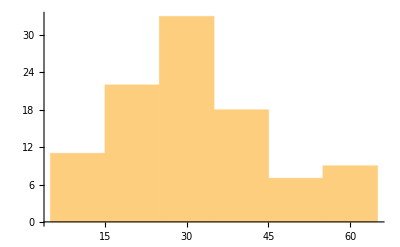

```mathematica
Histogram[%27]
```